```mathematica
1
```

1

```mathematica
N[Table[(1+1/10^k)^(10^k),{k,1,6}],10]
```

{2.59374246,2.704813829,2.716923932,2.718145927,2.718268237,2.718280469}

```mathematica
N[Table[(E-(1+1/10^k)^(10^k)),{k,1,6}]]
```

{0.124539,0.013468,0.0013579,0.000135902,0.0000135913,1.35914×10^-6}

```mathematica
(*Factorial*)

Table[Factorial[n],{n,0,20}]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000}

```mathematica
(*Factorial*)

Table[Factorial[n],{n,-2,2}]
```

{ComplexInfinity,ComplexInfinity,1,1,2}

```mathematica
Sort[{ComplexInfinity,ComplexInfinity,1,1,2}]
```

{1,1,2,ComplexInfinity,ComplexInfinity}

```mathematica
AbsoluteTiming[Table[n!,{n,1,20}]]
```

{0.0000248,{1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000}}

```mathematica
First[{0.0000248,{1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000}}]
```

0.0000248

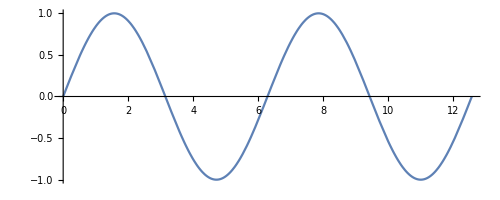

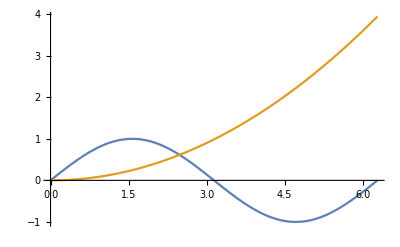

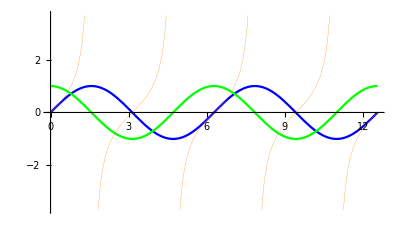

```mathematica
Plot[Sin[x],{x,0,4Pi},AspectRatio->Automatic]
Plot[{Sin[x],x^2 / 10} ,{x,0,2Pi}]
Plot[{Sin[x],Cos[x],Tan[x]},{x,0,4Pi},
PlotStyle->{{Blue},{Green},{Orange,Thickness[0.0005]}},
AspectRatio->Automatic]
```

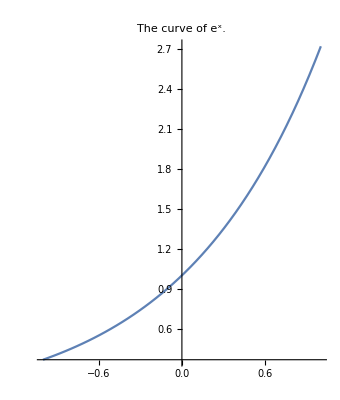

```mathematica
Plot[E^x,{x,-1,1},
AspectRatio->Automatic,
PlotLabel->"The curve of e^x."]
```

```mathematica
GoldenRatio
```

GoldenRatio

```mathematica
RootReduce[GoldenRatio]
```

1/2 (1+√5)

```mathematica
N[1/2 (1+√5)]
```

1.61803

```mathematica
RealDigits[1.618033988749895]
```

{{1,6,1,8,0,3,3,9,8,8,7,4,9,8,9,5},1}

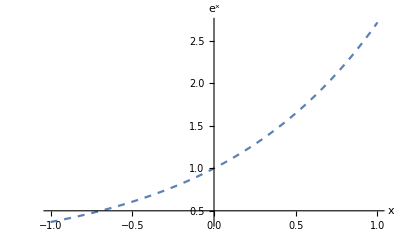

```mathematica
Plot[E^x,{x,-1,1},AxesOrigin->{0,0.5},AxesLabel->{x,e^x},
PlotStyle->Dashed]
```

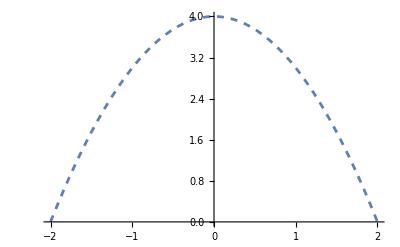

```mathematica
Plot[(4-x^2),{x,-2,2},PlotStyle->{Dashed,Thickness[0.005]}]
```

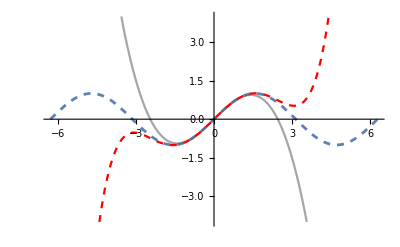

```mathematica
Plot[{Sin[x],x-x^3/(3!),x-x^3/(3!)+x^5/(5!)},{x,-2Pi,2Pi},
PlotStyle->{{Dashed,Thickness[0.005]},{GrayLevel[0.38,0.56],Thickness[0.004]},{Red,Dashed}}]
```

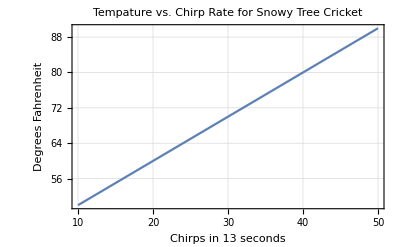

```mathematica
(* using Gridline , Frame and FrameLabel *)
Plot[x+40,{x,10,50},PlotLabel->"Tempature vs. Chirp Rate for Snowy Tree Cricket",
GridLines->Automatic,Frame->True,
FrameLabel->{"Chirps in 13 seconds","Degrees Fahrenheit"},
LabelStyle->Bold]
```

```mathematica
(*example of Ticks*)
Plot[Sin[x],{x,-2Pi,2Pi},
Ticks->{Table[k Pi/2,{k,-4,4}],Table[k,{k,-1,1,0.5}]} ]
```

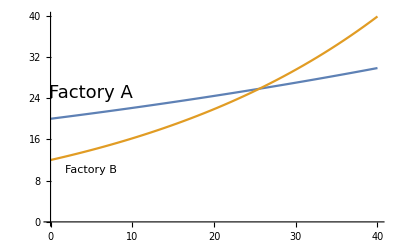

```mathematica
(*using Epilog to add labels*)
Plot[{20 E^(0.01t) ,12 E^(0.03t)},{t,0,40},
AxesOrigin->{0,0},
Epilog->{Text[Style["Factory A",FontSize->18],{5,25}],Text["Factory B",{5,10}]}]
```

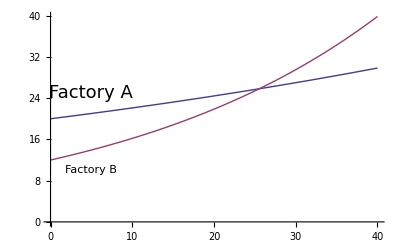

```mathematica
Plot[{20 ⅇ^(0.01 t),12 ⅇ^(0.03 t)},{t,0,40},PlotTheme->"Classic",AxesOrigin->{0,0},Epilog->{Text[Style["Factory A",FontSize->18],{5,25}],Text["Factory B",{5,10}]}]
```

```mathematica
Plot[{Tooltip[20 ⅇ^(0.01 t),"Factory A"],Tooltip[12 ⅇ^(0.03 t),"Factory B"]},{t,0,40},PlotTheme->"Classic",AxesOrigin->{0,0}]
```

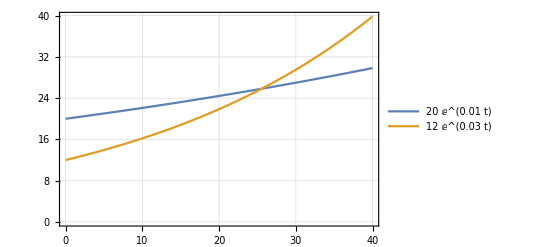

```mathematica
Plot[{Tooltip[20 ⅇ^(0.01 t),"Factory A"],Tooltip[12 ⅇ^(0.03 t),"Factory B"]},{t,0,40},PlotTheme->"Detailed",AxesOrigin->{0,0}]
```

```mathematica
(*using manipulate for animation*)

Manipulate[
Plot[(x^3+a x+4),{x,-8,8},
PlotRange->{{-8,8},{-100,100}},
AspectRatio->1
],
{a,-10,10}
]
```

```mathematica
Manipulate[Plot[x^3+a x+4,{x,-8,8},PlotRange->{{-8,8},{-100,100}},AspectRatio->1],{a,-10,10},Paneled->False]
```

```mathematica
Manipulate[
Plot[
{Tooltip[Sin[x]^n,"Sine"],Tooltip[Cos[x]^n,"Cosine"]},{x,-4Pi,4Pi},
PlotRange->{{-4Pi,4Pi},Automatic},
AspectRatio->1],
{n,1,5,1}
]
```

```mathematica
Manipulate[
Plot[
{Tooltip[Tan[x]^n,"Tan"],Tooltip[Cot[x]^n,"Cot"]},{x,-4Pi,4Pi},
PlotRange->{{-4Pi,4Pi},Automatic},
AspectRatio->1],
{n,1,5,1}
]
```

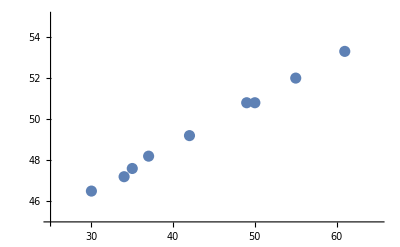

```mathematica
(*Plotting points with Listplot*)
(*Plotting from discrete data *)

chirpdata = {{30,46.5},{34,47.2},{35,47.6},{37,48.2},{42,49.2},{49,50.8},{50,50.8},{55,52.0},{61,53.3}};
dataPlot = ListPlot[chirpdata,PlotRange->{{25,65},{45,55}},
AxesOrigin->{25,45},PlotStyle->PointSize[0.02]]
```

```mathematica
(*datafitting*)

Fit[chirpdata,{1,x},x]
```

39.8931+0.220259 x

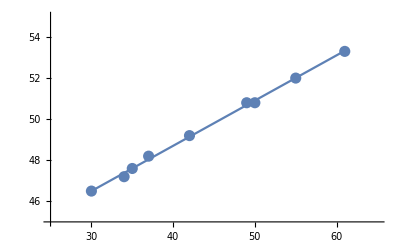

```mathematica
Show[dataPlot,Plot[39.89312345679015+0.2202592592592588x,{x,30,61}]
]
```

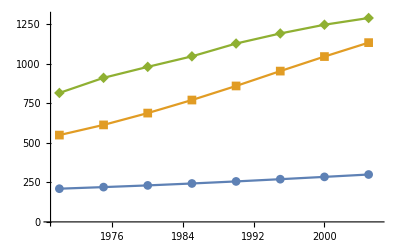

```mathematica
(*using listplot to plot datapoints*)

usdata = {{1970,210.111},{1975,220.165},{1980,230.917},{1985,243.063},{1990,256.098},{1995,270.245},{2000,284.857},{2005,299.846}};
indiadata = {{1970,549.317},{1975,613.767},{1980,688.575},{1985,771.121},{1990,860.195},{1995,954.282},{2000,1046.24},{2005,1134.4}};
chinadata = {{1970,815.999},{1975,911.658},{1980,981.072},{1985,1047.59},{1990,1128.67},{1995,1192.37},{2000,1247.69},{2005,1290.21}};

ListPlot[{usdata,indiadata,chinadata},
AxesOrigin->{1969,0}, PlotRange->{{1969,2006},{0,1300}},
PlotMarkers->Automatic , Joined->True
]
```

```mathematica
Fit[indiadata, {1,x,x^2},x]
```

306417.-324.533 x+0.0859226 x^2

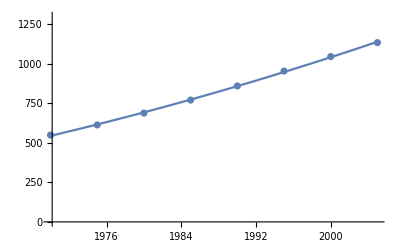

```mathematica
curveplot = Plot[306416.6346250556-324.53255119053097 x+0.08592261904763256 x^2,{x,1970,2005}];
dataPlot1 = ListPlot[indiadata,PlotRange->{{1970,2005},{0,1300}}];
Show[dataPlot1,curveplot]
```

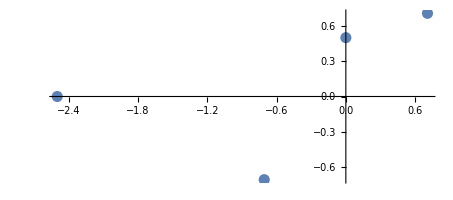

```mathematica
(*plotting points in polar coordinates*)

ListPolarPlot[{{Pi/4,1},{Pi/2,0.5},{0,-2.5},{-(3Pi)/4,1}},
PlotStyle->PointSize[0.02],AspectRatio->Automatic]
```

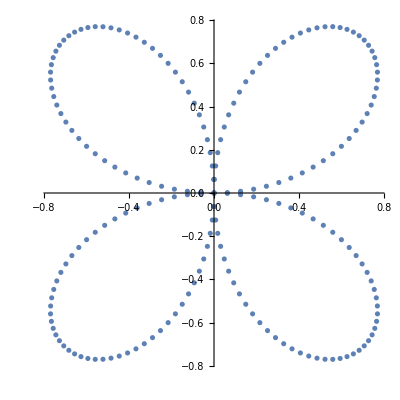

```mathematica
ListPolarPlot[Table[{θ,Sin[2θ]},{θ,0,2π,π/100}]
]
```

```mathematica
Manipulate[PolarPlot[{Sin[n θ],Cos[m θ]+Sin[m θ]},{θ,0,2π}],{n,1,10,1},{m,1,10,1}]
```